# Sustain Compressor

## First order lowpass filter

```mathematica
firstOrderLowpass[X_,fc_,sampleRate_]:=Module[{γ, a0, a1, b0, b1,out,i,za,zb},
out = X;

Assert[fc <sampleRate/2];

γ = N[Tan[ π fc / sampleRate]];
a0 = γ + 1;
b0 = γ / a0;
b1 = b0;
a1 = (γ-1)/a0;

za = 0;
zb = 0;

For[i=1,i≤Length[X],i++,
out[[i]] = b0 X[[i]] + b1 zb - a1 za;
za = out[[i]];
zb = X[[i]];
];

out
]
```

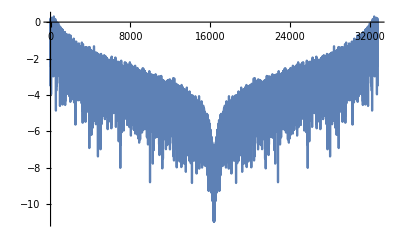

```mathematica
(* test *)
ListLinePlot[
Log[Abs[Fourier[
firstOrderLowpass[RandomReal[{-1,1},4096*8],1000,48000]
]]]
]
```

## Compressor tests

The basic idea is to have several stages of compression with different thresholds. Compressors with lower thresholds have longer attack and release times. This results in a kind of saturating limiter but with much lower harmonic distortion. 

For now we simply use lowpass filters to compute the volume envelope, so that the attack and release times are equal.

## Limiter unit

A single stage limiter unit consists of an envelope follower and a gain reduction that attenuates the output if it exceeds a given threshold.

```mathematica
dBToGain[dB_]:=10^(dB/20)
gainToDb[g_]:=20 Log10[g]
ramp[x_]:=(x +Abs[x])/2

lowpassSVF[X_,fc_,sr_]:=Module[{Q,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
ic1 = ic2 = v1 = v2 = v3 = 0;
ic2 = 1;

For[i=1, i<=Length[X], i++,
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

output
]

limiterUnit[X_,thresholdDb_,fc_,sampleRate_]:=Module[{envelope, envelopeDb, excessDb,gainReductionDb, controlSignal},
envelope = 
lowpassSVF[
lowpassSVF[
lowpassSVF[Abs[X],fc, sampleRate],
fc,sampleRate],
fc, sampleRate];

envelopeDb = gainToDb[envelope];
excessDb = ramp[envelopeDb - thresholdDb];
gainReductionDb = -excessDb;
controlSignal = dBToGain[gainReductionDb];

X * controlSignal
]

asymptoticLimit[X_]:=X / (1+ Abs[X])

limiterUnit2[X_,fc_,sampleRate_]:=Module[{envelope,limitedEnvelope,controlSignal},
envelope = 
lowpassSVF[
lowpassSVF[
lowpassSVF[Abs[X],fc, sampleRate],
fc,sampleRate],
fc, sampleRate];

limitedEnvelope = asymptoticLimit[envelope];
controlSignal = (limitedEnvelope+ 0.0001) / (envelope+ 0.0001);

X * controlSignal
]
```

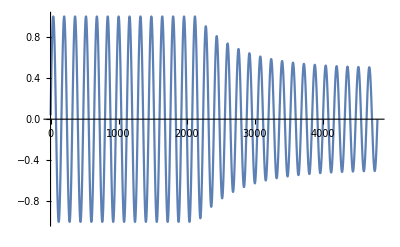

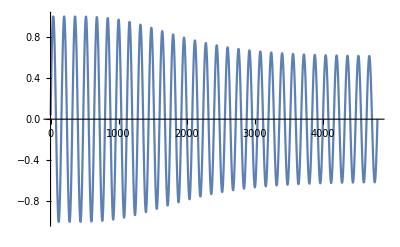

```mathematica
(* test limiter unit *)
freq = 300;
sampleRate =48000;
fc = 20;
thresholdDb = -10;
testInput = Table[Sin[freq 2π t / sampleRate],{t,1,0.1 sampleRate}];
testOutput = limiterUnit[testInput,thresholdDb,fc,sampleRate];
ListLinePlot[testOutput,PlotRange->All]
testOutput = limiterUnit2[testInput,fc,sampleRate];
ListLinePlot[testOutput,PlotRange->All]
```

## Multi-stage limiter

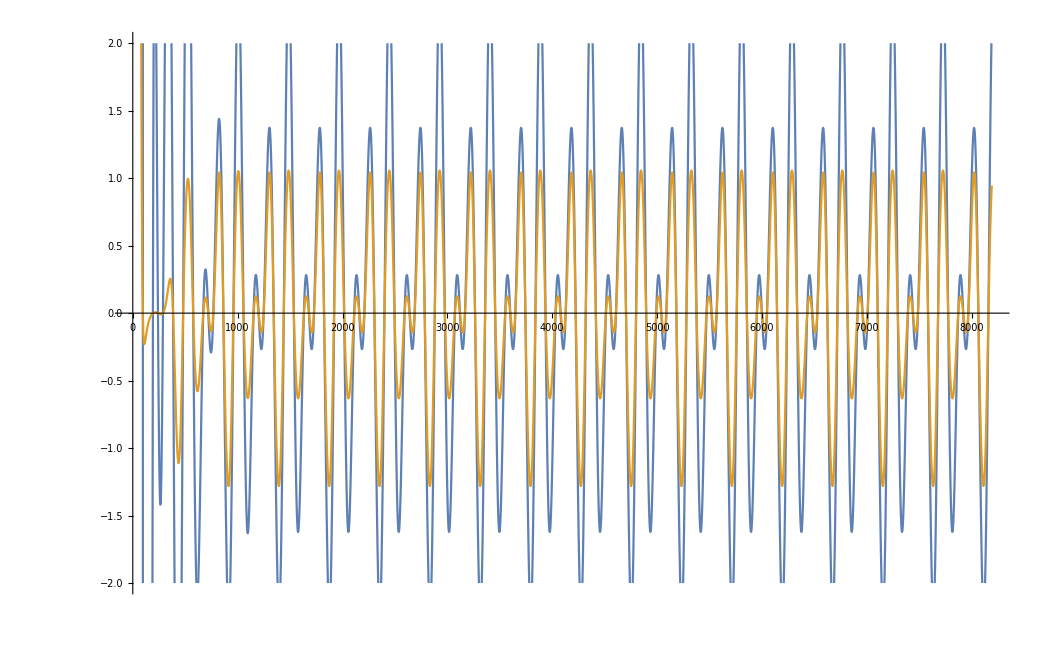

-Graphics-

-Graphics-

```mathematica
freq = 200;
sampleRate =48000;
fc = 100;
thresholdDb = -6;
inputGainDb = 60;
length = 2^13;
testInput =dBToGain[inputGainDb] Table[2^(N[-2t]/sampleRate)(Sin[freq 2π N[t] / sampleRate]+Sin[(3/2)freq 2π N[t] / sampleRate]),{t,1,length}];

mp = 4;

testOutput1 =
limiterUnit2[testInput,fc,sampleRate];


testOutput2 =
limiterUnit2[
limiterUnit2[testInput,fc,sampleRate],
mp fc,sampleRate];

ListLinePlot[{testOutput1,testOutput2},PlotRange->{-2,2}]
ListPlay[testInput, SampleRate->sampleRate]
ListPlay[testOutput2, SampleRate->sampleRate]
```

## Attack Transient Softener

```mathematica
releaseOnlySVF[X_,fc_,sr_]:=Module[{Q,prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]



attackOnlySVF[X_,fc_,sr_]:=Module[{prevY,prevY2,Q,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
Q=0.5;
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]

takeNegative[X_]:=(X -Abs[X])/2
upperLimit[X_,limit_]:=takeNegative[X-limit]+limit

attackSoftener[X_,sampleRate_]:=Module[{b1, b2,b3,b4, attackFc, releaseFc,attackReduction},
(* set attack time and release time *)
attackFc = 25;
releaseFc = 25;
attackReduction = 1;

(* generate volume envelope *)
b1 = Abs[X];
b1 = upperLimit[b1,1]; (* by clipping the envelope at 1, we prevent it from reacting to enormous peaks at note start *)
b2 = lowpassSVF[b1,attackFc,sampleRate]; 

(* find the ratio that X has to be reduced in order to force it beneath the envelope *)
b3 = b2 / (Abs[X]+ 0.0001);
b3 = upperLimit[b3,1];

(* filter the control signal to reduce aliasing *)
b4 = releaseOnlySVF[b3,releaseFc,sampleRate];
(* b4 = lowpassSVF[b4,attackFc,sampleRate]; *)
(* b4 = b3; *)

(* force X to fit beneath the envelope *)
{b2, b3, b4, X*b4^(attackReduction)}
]
```

## Attack softener combined with limiter

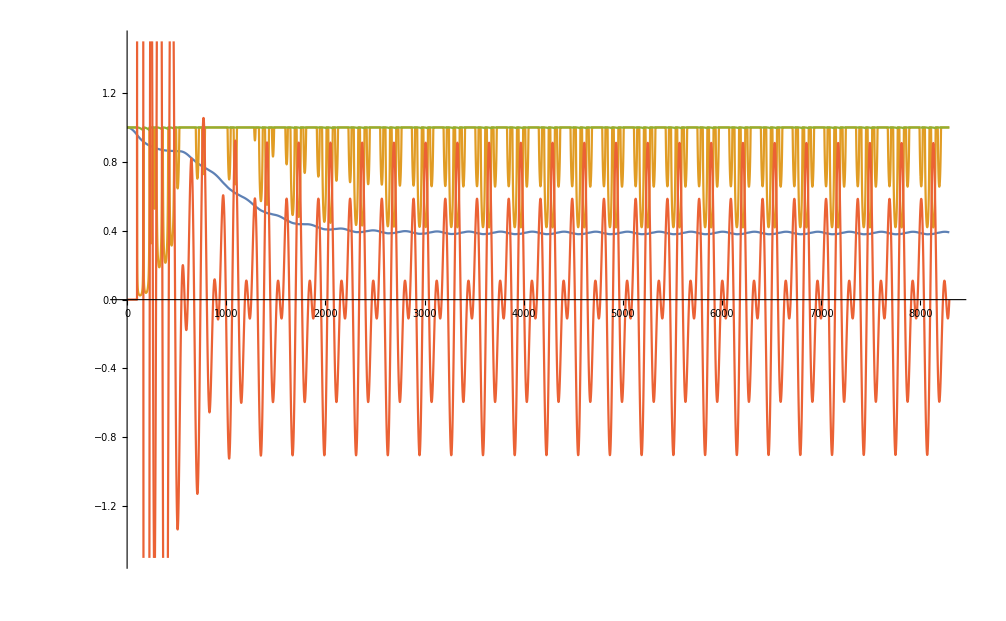

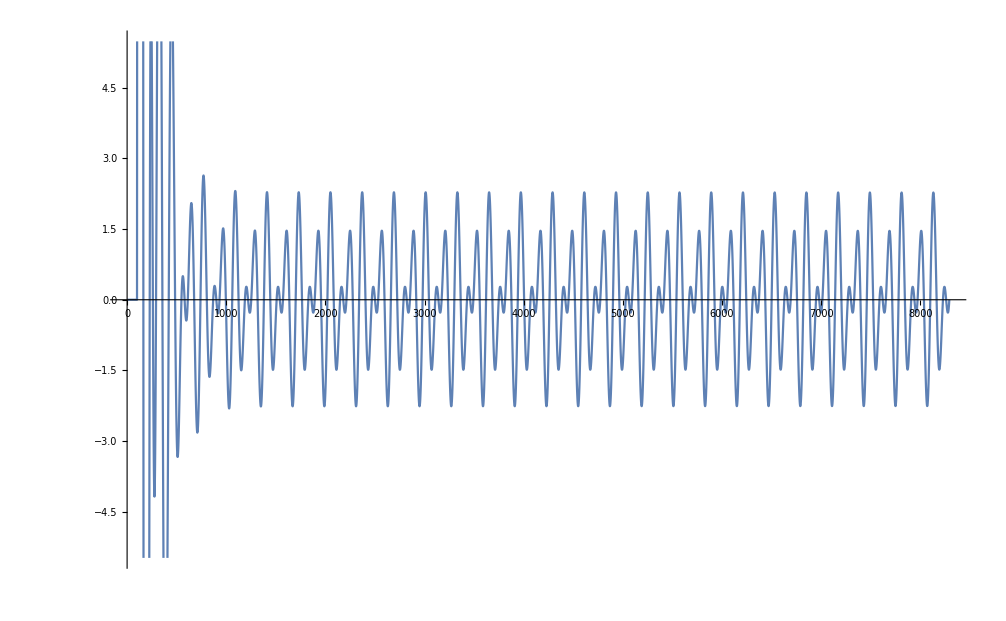

```mathematica
freq = 300;
sampleRate =48000;
fc = 100;
thresholdDb = -6;
inputGainDb = 40;
length = 2^13;
testInput =Join[0Range[100],dBToGain[inputGainDb] Table[2^(N[-2t]/sampleRate)(Sin[freq 2π N[t] / sampleRate]+Sin[(3/2)freq 2π N[t] / sampleRate]),{t,1,length}]
];
(* testInput = Join[testInput,0Range[10000]]+Join[0Range[10000],testInput]; *)

testOutput1 =limiterUnit2[testInput,fc,sampleRate];
testOutput2 = attackSoftener[0.4limiterUnit2[testInput,fc,sampleRate],sampleRate];

(* ListLinePlot[{testOutput1, testOutput2},PlotRange->4{-1,1}] *)
ListLinePlot[testOutput2,PlotRange->1.5{-1,1}]
ListLinePlot[testOutput1]
```

```mathematica
(* convert to a sound *)
audioObject1 = Sound[ListPlay[testInput,SampleRate->48000,PlayRange->All]]
audioObject2 = Sound[ListPlay[testOutput1,SampleRate->48000, PlayRange->4{-1,1}]]
audioObject3 = Sound[ListPlay[testOutput2[[4]],SampleRate->48000, PlayRange->4{-1,1}]]

(* save to audio file *)
Export["~/Desktop/testInput.wav",audioObject1,AudioEncoding->"Integer24"]
Export["~/Desktop/testOutput1.wav",audioObject2,AudioEncoding->"Integer24"]
Export["~/Desktop/testOutput2.wav",audioObject3,AudioEncoding->"Integer24"]
```

-Graphics-

-Graphics-

-Graphics-

~/Desktop/testInput.wav

~/Desktop/testOutput1.wav

~/Desktop/testOutput2.wav